```mathematica
EJ=2618.942;
EL=2.5EJ;
nmax=5;
nlistname=Table[(ToString[n])<>" JJs / Arm",{n,1,nmax}];
HJ=-n^2 EJ(Cos[Subscript[φ, a]/n]+Cos[Subscript[φ, b]/n]+Cos[Subscript[φ, c]/n]+Cos[Subscript[φ, d]/n]-4);
Hshunt=EL/2(Subscript[φ, L1]^2+Subscript[φ, L2]^2+Subscript[φ, L3]^2+Subscript[φ, L4]^2);
({{Subscript[φ, a]}, {Subscript[φ, b]}, {Subscript[φ, c]}, {Subscript[φ, d]}})=({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{Subscript[φ, x]}, {Subscript[φ, y]}, {Subscript[φ, z]}, {Subscript[φ, M]}});
solvecros=Flatten[Simplify[Solve[Subscript[φ, a]-Subscript[φ, L1]+Subscript[φ, L2]==Subscript[φ, ext]/4+2Pi Subscript[n, a]&&Subscript[φ, b]-Subscript[φ, L2]+Subscript[φ, L3]==Subscript[φ, ext]/4+2Pi Subscript[n, b]&&Subscript[φ, c]-Subscript[φ, L3]+Subscript[φ, L4]==Subscript[φ, ext]/4+2Pi Subscript[n, c]&&Subscript[φ, L1]+Subscript[φ, L2]+Subscript[φ, L3]+Subscript[φ, L4]==0,{Subscript[φ, L1],Subscript[φ, L2],Subscript[φ, L3],Subscript[φ, L4]}]/.Subscript[φ, M]->Subscript[φ, ext]+2Pi(Subscript[n, a]+Subscript[n, b]+Subscript[n, c]+Subscript[n, d])]/.{Subscript[n, a]->m,Subscript[n, b]->m,Subscript[n, c]->m,Subscript[n, d]->m}];
Hshunt=Simplify[Hshunt/.solvecros];
HJ=Simplify[HJ/.Subscript[φ, M]->Subscript[φ, ext]];
Htot=Simplify[HJ+Hshunt]
```

n^2 (10475.8-10475.8 Cos[φ_ext/(4 n)] Cos[φ_x/(2 n)] Cos[φ_y/(2 n)] Cos[φ_z/n]-10475.8 Sin[φ_ext/(4 n)] Sin[φ_x/(2 n)] Sin[φ_y/(2 n)] Sin[φ_z/n])+1636.84 φ_x^2+1636.84 φ_y^2+3273.68 φ_z^2

```mathematica
H[ϕx_,ϕy_,ϕz_,ϕext_,n_,EJ_,EL_]:=-4 EJ n^2 (-1+Cos[ϕext/(4 n)] Cos[ϕx/(2 n)] Cos[ϕy/(2 n)] Cos[ϕz/n]+Sin[ϕext/(4 n)] Sin[ϕx/(2 n)] Sin[ϕy/(2 n)] Sin[ϕz/n])+1/4 EL (ϕx^2+ϕy^2+2 ϕz^2)
```

```mathematica
ip=Table[RandomReal[{0.,20π},3],50];

Monitor[For[listEmin={};n=1,n≤nmax,n++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,ip[[i,1]]},{ϕy,ip[[i,2]]},{ϕz,ip[[i,3]]}]];
{res[[1]],ϕx,ϕy,ϕz}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π, π/5}]
,ϕext];
listEmin=Insert[listEmin,t1,n]
],
n]
```

### Plot E_min as a function of ϕ_ext

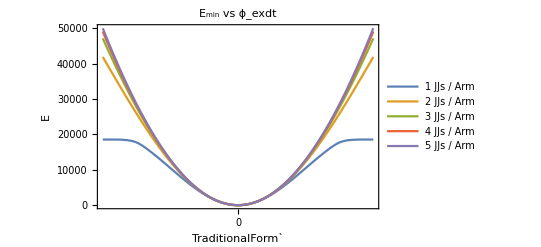

```mathematica
itpEmin[n_]:=Interpolation[listEmin[[n,All,1,{1,2}]]];
Plot[
Evaluate[Table[itpEmin[n][x],{n,1,nmax}],{x,-4π,4π}], Frame->True, FrameLabel->{"TraditionalForm`","E"}, FrameTicks->{Automatic,{2π Range[-10,10],None}},PlotLegends->nlistname,PlotLabel->Style["E_min vs ϕ_exdt",Bold, 16,Orange]
]
```

```mathematica
ϕnode[n_,j_]:=Flatten[({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{listEmin[[n,j,1,3]]}, {listEmin[[n,j,1,4]]}, {listEmin[[n,j,1,5]]}, {listEmin[[n,j,1,1]]}})]
ϕnode[2,2]-

ϕarm[n_,i_]:=Table[{π Range[-4,4, 1/5][[j]],ϕnode[n,j][[If[i<4,i+1,1]]]-ϕnode[n,j][[i]]},{j,1,Length[listEmin[[n]]]}]
```

{-2.98451,-2.98451,-2.98451,-2.98451}

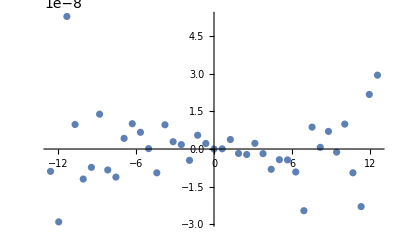

```mathematica
ListPlot[ ϕarm[2,2],PlotRange->All]
```

### Find Derivatives

#### Discuss (ϕx,ϕy,ϕz) at the extreme points

```mathematica
ϕzmin[n_]:=Table[{listEmin[[n,k,1,1]],Abs[listEmin[[n,k,1,5]]]},{k,1,Length[listEmin[[n]]]}]
itpϕzmin[n_]:=Interpolation[ϕzmin[n]]
itpϕzmin[1][-20 π]
```

1.59935

#### Calculate the Derivatives

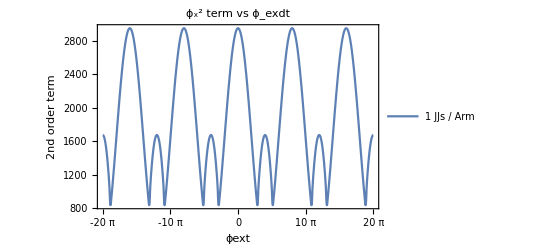

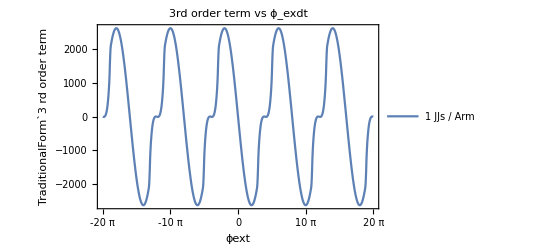

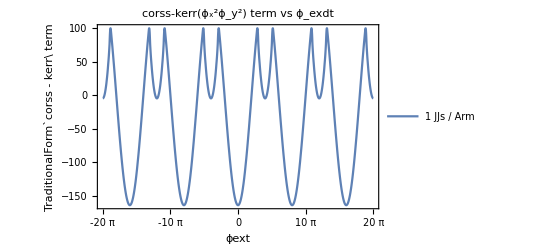

```mathematica
x2[ϕext_,n_]:=1/2 D[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,2}]/.{ϕx->0,ϕy->0,ϕz->itpϕzmin[n][ϕext]};
xyz[ϕext_,n_]:=D[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,1},{ϕy,1},{ϕz,1}]/.{ϕx->0,ϕy->0,ϕz->itpϕzmin[n][ϕext]};
x2y2[ϕext_,n_]:=1/4 D[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,2},{ϕy,2}]/.{ϕx->0,ϕy->0,ϕz->itpϕzmin[n][ϕext]};x4[ϕext_,n_]:=1/24 D[H[ϕx,ϕy,ϕz,ϕext,n,EJ,EL],{ϕx,4}]/.{ϕx->0,ϕy->0,ϕz->itpϕzmin[n][ϕext]};
Plot[Evaluate[Table[x2[ϕext,n],{n,1,1}]],{ϕext,-20π,20π}, Frame->True, FrameLabel->{"ϕext","2nd order term"}, FrameTicks->{Automatic,{2π Range[-10,10],None}},PlotLegends->nlistname,PlotLabel->Style["ϕ_x^2 term vs ϕ_exdt",Bold, 16,Orange]]

Plot[Evaluate[Table[xyz[ϕext,n],{n,1,1}]],{ϕext,-20π,20π}, Frame->True, FrameLabel->{"ϕext","TraditionalForm`3  rd order term"}, FrameTicks->{Automatic,{2π Range[-10,10],None}},PlotLegends->nlistname,PlotLabel->Style["3rd order term vs ϕ_exdt",Bold, 16,Orange]]

Plot[Evaluate[Table[x2y2[ϕext,n],{n,1,1}]],{ϕext,-20π,20π}, Frame->True, FrameLabel->{"ϕext","TraditionalForm`corss - kerr\ term"}, FrameTicks->{Automatic,{2π Range[-10,10],None}},PlotLegends->nlistname,PlotRange->All,PlotLabel->Style["corss-kerr(ϕ_x^2ϕ_y^2) term vs ϕ_exdt",Bold, 16,Orange]]
```

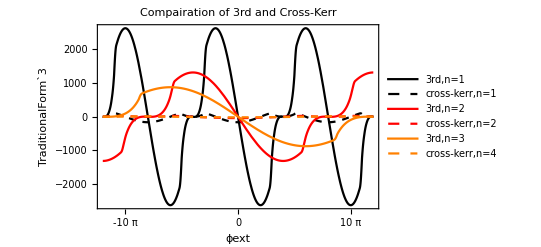

```mathematica
Plot[Evaluate[Table[{xyz[ϕext,n],x2y2[ϕext,n]},{n,1,3}]],{ϕext,-12π,12π}, Frame->True, FrameLabel->{"ϕext","TraditionalForm`3"}, FrameTicks->{Automatic,{2π Range[-10,10],None}},PlotLegends->{"3rd,n=1","cross-kerr,n=1","3rd,n=2","cross-kerr,n=2","3rd,n=3","cross-kerr,n=4"},PlotRange->All,PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed},Orange,{Orange,Dashed}},PlotLabel->Style["Compairation of 3rd and Cross-Kerr",Bold, 16,Orange]]
```

```mathematica
ϕextlist=Table[π i,{i,-20,20,0.11}];
len1=Length[ϕextlist];
ratiolist=Table[x2y2[ϕextlist[[i]],n]/xyz[ϕextlist[[i]],n],{i,1,len1},{n,1,nmax}];
laratiolist=Flatten[Table[{ϕextlist[[i]],n,Log10[Abs[ratiolist[[i,n]]]]},{i,1,len1},{n,1,nmax}],1];
```

```mathematica
Needs["ColorBar`"]
ColorBar[]
```

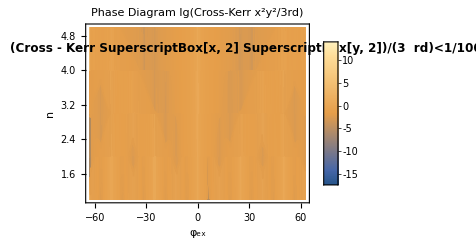

```mathematica
ldp=ListDensityPlot[
laratiolist,
PlotLegends->Placed[Automatic,Right],FrameLabel->{"φ_ex","n"},
FrameStyle->Directive[Thick,14],FrameTicks->{Automatic,Automatic},PlotLabel->Style["Phase Diagram\nlg(Cross-Kerr x^2y^2/3rd)",Bold, 16,Orange],PlotRange->All,Mesh->1,MeshStyle->Black,MeshFunctions->{Boole[Greater[#3,-2]]&},AspectRatio->0.6
];


Show[ldp,Graphics[Text[Style["(Cross - Kerr SuperscriptBox[x, 2] SuperscriptBox[y, 2])/(3  rd)<1/100",12,Bold],{28,4.5}]]]
```